```mathematica
FullSimplify[(  ArcTanh[(a+b r^2)/(2 √(a b) √(r^2+2 a p^2 b r^2-a^2 p^2-b^2 p^2 r^4))])/(2 √(a b))]
```

ArcTanh[(a+b r^2)/(2 √(a b) √(-(a p+r-b p r^2) (a p-r (1+b p r))))]/(2 √(a b))

```mathematica
Solve[(r^2+2 a p^2 b r^2-a^2 p^2-b^2 p^2 r^4)==0,r]
```

{{r→(-1-√(1+4 a b p^2))/(2 b p)},{r→(1-√(1+4 a b p^2))/(2 b p)},{r→(-1+√(1+4 a b p^2))/(2 b p)},{r→(1+√(1+4 a b p^2))/(2 b p)}}

```mathematica
FullSimplify[((1-√(1+4 a b p^2))/(2 b p))^2]
```

((-1+√(1+4 a b p^2))^2)/(4 b^2 p^2)

```mathematica
((-1+√(1+4 a b p^2))^2)/(4 b^2 p^2)<r^2<((1+√(1+4 a b p^2))^2)/(4 b^2 p^2)
```

```mathematica
(p^2 a)/(1+p^2 b)<r^2
```

```mathematica
Solve[s==(  ArcTanh[(a+b r^2)/(2 √(a b) √(r^2+2 a p^2 b r^2-a^2 p^2-b^2 p^2 r^4))])/(2 √(a b)),r]
```

{{r→-√(-(a b)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(2 a b Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(4 a^2 b^2 p^2 Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)-(2 √(a^2 b^2 (1+4 a b p^2) Tanh[(2 a b s)/(√(a b))]^2 (-1+Tanh[(2 a b s)/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2))},{r→√(-(a b)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(2 a b Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(4 a^2 b^2 p^2 Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)-(2 √(a^2 b^2 (1+4 a b p^2) Tanh[(2 a b s)/(√(a b))]^2 (-1+Tanh[(2 a b s)/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2))},{r→-√(-(a b)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(2 a b Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(4 a^2 b^2 p^2 Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(2 √(a^2 b^2 (1+4 a b p^2) Tanh[(2 a b s)/(√(a b))]^2 (-1+Tanh[(2 a b s)/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2))},{r→√(-(a b)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(2 a b Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(4 a^2 b^2 p^2 Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(2 √(a^2 b^2 (1+4 a b p^2) Tanh[(2 a b s)/(√(a b))]^2 (-1+Tanh[(2 a b s)/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2))}}

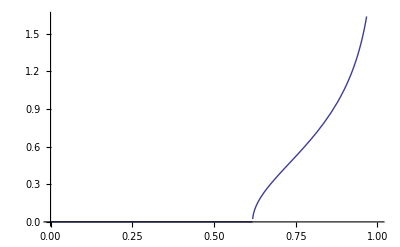

```mathematica
a=1;
b=1;
p=1;
Plot[{Re[(  ArcTanh[(a+b r^2)/(2 √(a b) √(r^2+2 a p^2 b r^2-a^2 p^2-b^2 p^2 r^4))])/(2 √(a b))]},{r,0,Sqrt[a/b]}]
```

```mathematica
s+c=ArcTanh[(a+b r^2)/(2 √(a b) √(r^2+2 a p^2 b r^2-a^2 p^2-b^2 p^2 r^4))]/(2 √(a b))
```

```mathematica
(2 √(a b) √(r^2+2 a p^2 b r^2-a^2 p^2-b^2 p^2 r^4))Tanh[2 √(a b)(s+c)]=(a+b r^2)
```

```mathematica
4 √(a b) (r^2+2 a p^2 b r^2-a^2 p^2-b^2 p^2 r^4)(Tanh^2)[2 √(a b)(s+c)]=(a+b r^2)^2
```

```mathematica
4 √(a b) (r^2+2 a p^2 b r^2-a^2 p^2-b^2 p^2 r^4)(Tanh^2)[2 √(a b)(s+c)]=a^2+2a b r^2+b^2 r^4
```

```mathematica
-(4 √(a b)a^2 p^2(Tanh^2)[2 √(a b)(s+c)]+a^2)+(4 √(a b)(1+2 a p^2 b )(Tanh^2)[2 √(a b)(s+c)]-2a b)r^2-(4 √(a b)b^2 p^2(Tanh^2)[2 √(a b)(s+c)] -b^2)r^4=0
```

```mathematica
r^2=1/(2(4 √(a b)b^2 p^2(Tanh^2)[2 √(a b)(s+c)] -b^2))(-(4 √(a b)(1+2 a p^2 b )(Tanh^2)[2 √(a b)(s+c)]-2a b)+Sqrt[(4 √(a b)(1+2 a p^2 b )(Tanh^2)[2 √(a b)(s+c)]-2a b)^2+4(4 √(a b)a^2 p^2(Tanh^2)[2 √(a b)(s+c)]+a^2)(4 √(a b)b^2 p^2(Tanh^2)[2 √(a b)(s+c)] -b^2)])
```

```mathematica
FullSimplify[1/(2(4 √(a b)b^2 p^2(Tanh^2)[2 √(a b)(s+c)] -b^2))(-(4 √(a b)(1+2 a p^2 b )(Tanh^2)[2 √(a b)(s+c)]-2a b)+Sqrt[(4 √(a b)(1+2 a p^2 b )(Tanh^2)[2 √(a b)(s+c)]-2a b)^2+4(4 √(a b)a^2 p^2(Tanh^2)[2 √(a b)(s+c)]+a^2)(4 √(a b)b^2 p^2(Tanh^2)[2 √(a b)(s+c)] -b^2)])]
```

```mathematica
(a b-2 √(a b) (1+2 a b p^2) (Tanh^2)[2 √(a b) (c+s)]+2 √(a b (Tanh^2)[2 √(a b) (c+s)] (-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)])))/(b^2 (-1+4 √(a b) p^2 (Tanh^2)[2 √(a b) (c+s)]))
```

```mathematica
a=1;
b=1;
c=0;
p=1;
```

```mathematica
r[s_]:=Sqrt[(a b-2 √(a b) (1+2 a b p^2) (Tanh^2)[2 √(a b) (c+s)]+2 √(a b (Tanh^2)[2 √(a b) (c+s)] (-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)])))/(b^2 (-1+4 √(a b) p^2 (Tanh^2)[2 √(a b) (c+s)]))]
```

```mathematica
FullSimplify[p v[r[s]]^2/r[s]^2]
```

```mathematica
Integrate[(b^2 p (-1+4 √(a b) p^2 (Tanh^2)[2 √(a b) (c+s)]) v[√((a b-2 √(a b) (1+2 a b p^2) (Tanh^2)[2 √(a b) (c+s)]+2 √(a b (Tanh^2)[2 √(a b) (c+s)] (-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)])))/(b^2 (-1+4 √(a b) p^2 (Tanh^2)[2 √(a b) (c+s)])))]^2)/(a b-2 √(a b) (1+2 a b p^2) (Tanh^2)[2 √(a b) (c+s)]+2 √(a b (Tanh^2)[2 √(a b) (c+s)] (-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)]))),s]
```

```mathematica
v[r_]:=a-b r^2
```

```mathematica
FullSimplify[p v[r[s]]^2/r[s]^2]
```

-(4 p (-a b+8 a^2 b^2 p^4 (Tanh^2[2 √(a b) (c+s)])^2+√(a b) Tanh^2[2 √(a b) (c+s)] (1+2 p^2 (a b-2 √(a b Tanh^2[2 √(a b) (c+s)] (-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) Tanh^2[2 √(a b) (c+s)]))))))/(-1+16 a b p^4 (Tanh^2[2 √(a b) (c+s)])^2)

```mathematica
-(4 p (-a b+8 a^2 b^2 p^4 ((Tanh^2)[2 √(a b) (c+s)])^2+√(a b) (Tanh^2)[2 √(a b) (c+s)] (1+2 p^2 (a b-2 √(a b (Tanh^2)[2 √(a b) (c+s)] (-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)]))))))/(-1+16 a b p^4 ((Tanh^2)[2 √(a b) (c+s)])^2)
```

```mathematica
a=1
b=1
c=0
p=1
```

1

1

0

1

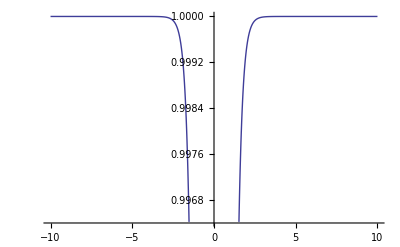

```mathematica
Plot[{Re[(-(a b)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(2 a b Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)+(4 a^2 b^2 p^2 Tanh[(2 a b s)/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2)-(2 √(a^2 b^2 (1+4 a b p^2) Tanh[(2 a b s)/(√(a b))]^2 (-1+Tanh[(2 a b s)/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tanh[(2 a b s)/(√(a b))]^2))],Re[1/(2(4 √(a b)b^2 p^2(Tanh^2)[2 √(a b)(s+c)] -b^2))(-(4 √(a b)(1+2 a p^2 b )(Tanh^2)[2 √(a b)(s+c)]-2a b)+Sqrt[(4 √(a b)(1+2 a p^2 b )(Tanh^2)[2 √(a b)(s+c)]-2a b)^2+4(4 √(a b)a^2 p^2(Tanh^2)[2 √(a b)(s+c)]+a^2)(4 √(a b)b^2 p^2(Tanh^2)[2 √(a b)(s+c)] -b^2)])]},{s,-10,10}]
```

```mathematica
FullSimplify[1/(2(4 √(a b)b^2 p^2(Tanh^2)[2 √(a b)(s+c)] -b^2))(-(4 √(a b)(1+2 a p^2 b )(Tanh^2)[2 √(a b)(s+c)]-2a b)+4Abs[ Tanh[2 √(a b) (c+s)] ]Sqrt[(-(a b)^(3/2) (1+2 a b p^2)+a b (1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)])])]
```

(a b-2 √(a b) (1+2 a b p^2) Tanh^2[2 √(a b) (c+s)]+2 Abs[Tanh[2 √(a b) (c+s)]] √(a b (-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) Tanh^2[2 √(a b) (c+s)])))/(b^2 (-1+4 √(a b) p^2 Tanh^2[2 √(a b) (c+s)]))

```mathematica
(a b-2 √(a b) (1+2 a b p^2) (Tanh^2)[2 √(a b) (c+s)]+2 √(a b) Abs[Tanh[2 √(a b) (c+s)]] √(-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)]))/(b^2 (-1+4 √(a b) p^2 (Tanh^2)[2 √(a b) (c+s)]))
```

```mathematica
v[r_]:=a-b r^2
```

```mathematica
r[s_]:=Sqrt[(a b-2 √(a b) (1+2 a b p^2) (Tanh^2)[2 √(a b) (c+s)]+2 √(a b) Abs[Tanh[2 √(a b) (c+s)]] √(-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)]))/(b^2 (-1+4 √(a b) p^2 (Tanh^2)[2 √(a b) (c+s)]))]
```

```mathematica
FullSimplify[v[r[s]]^2/r[s]^2]
```

-(4 (a b-√(a b) (1+4 a b p^2) Tanh^2[2 √(a b) (c+s)]+√(a b) Abs[Tanh[2 √(a b) (c+s)]] √(-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) Tanh^2[2 √(a b) (c+s)]))^2)/((-1+4 √(a b) p^2 Tanh^2[2 √(a b) (c+s)]) (-a b+2 √(a b) (1+2 a b p^2) Tanh^2[2 √(a b) (c+s)]-2 √(a b) Abs[Tanh[2 √(a b) (c+s)]] √(-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) Tanh^2[2 √(a b) (c+s)])))

```mathematica
a=1;
b=1;
c=0;
p=1;
```

```mathematica
FullSimplify[-(4 (a b-√(a b) (1+4 a b p^2) (Tanh^2)[2 √(a b) (c+s)]+√(a b) Abs[Tanh[2 √(a b) (c+s)]] √(-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)]))^2)/((-1+4 √(a b) p^2 (Tanh^2)[2 √(a b) (c+s)]) (-a b+2 √(a b) (1+2 a b p^2) (Tanh^2)[2 √(a b) (c+s)]-2 √(a b) Abs[Tanh[2 √(a b) (c+s)]] √(-√(a b) (1+2 a b p^2)+(1+4 a b p^2 (1+2 a b p^2)) (Tanh^2)[2 √(a b) (c+s)])))]
```

```mathematica
a=E
b=π
p=3^π
```

ⅇ

π

3^π

```mathematica
Integrate[(p v[r])/(r Sqrt[r^2-p^2 v[r]^2]),r]
```

1/2 (-ArcSin[(-1-2 9^π ⅇ π+2 9^π π^2 r^2)/(√(1+4 9^π ⅇ π))]+ArcTan[(2 3^π ⅇ √(-9^π ⅇ^2+r^2+2 9^π ⅇ π r^2-9^π π^2 r^4))/(2 9^π ⅇ^2-r^2-2 9^π ⅇ π r^2)])

```mathematica
a=E
b=π
p=3^π
```

```mathematica
θ[r_]:=1/2 (-ArcSin[(-1-2 p^2 a b+2 p^2 b^2 r^2)/(√(1+4 p^2 a b))]+ArcTan[(2 p a √(-p^2 a^2+r^2+2 p^2 a b r^2-p^2 b^2 r^4))/(2 p^2 a^2-r^2-2 p^2 a b r^2)])+θ0
```

```mathematica
FullSimplify[θ[r[s]],a>0&&b>0&&Element[{p,c},Reals]]
```

θ0+1/2 (-ArcSin[(1+4 a b p^2-8 √(a b) p^2 (1+2 a b p^2) Tanh^2[2 √(a b) (c+s)]+4 p^2 Abs[Tanh[2 √(a b) (c+s)]] √(a b (-√(a b) (1+2 a b p^2)+(1+4 a b p^2+8 a^2 b^2 p^4) Tanh^2[2 √(a b) (c+s)])))/(√(1+4 a b p^2) (-1+4 √(a b) p^2 Tanh^2[2 √(a b) (c+s)]))]+ArcTan[(2 a b^2 p (-1+4 √(a b) p^2 Tanh^2[2 √(a b) (c+s)]) √(-(a b (1+4 a b p^2)-2 √(a b) (1+4 a b p^2)^2 Tanh^2[2 √(a b) (c+s)]+4 a b p^2 (3+12 a b p^2+16 a^2 b^2 p^4) (Tanh^2[2 √(a b) (c+s)])^2+4 a b p^2 Abs[Tanh[2 √(a b) (c+s)]]^2 (-√(a b) (1+2 a b p^2)+(1+4 a b p^2+8 a^2 b^2 p^4) Tanh^2[2 √(a b) (c+s)])+2 Abs[Tanh[2 √(a b) (c+s)]] (-8 a b p^2 (1+2 a b p^2) Tanh^2[2 √(a b) (c+s)] √(-√(a b) (1+2 a b p^2)+(1+4 a b p^2+8 a^2 b^2 p^4) Tanh^2[2 √(a b) (c+s)])+(1+4 a b p^2) √(a b (-√(a b) (1+2 a b p^2)+(1+4 a b p^2+8 a^2 b^2 p^4) Tanh^2[2 √(a b) (c+s)]))))/(b-4 b √(a b) p^2 Tanh^2[2 √(a b) (c+s)])^2))/(-a b (1+4 a b p^2)+2 √(a b) (1+4 a b p^2+8 a^2 b^2 p^4) Tanh^2[2 √(a b) (c+s)]-2 (1+2 a b p^2) Abs[Tanh[2 √(a b) (c+s)]] √(a b (-√(a b) (1+2 a b p^2)+(1+4 a b p^2+8 a^2 b^2 p^4) Tanh^2[2 √(a b) (c+s)])))])